```mathematica
Clear["Global`*"];
```

### Compare Relic abundance for different NSI parameters

#### Plot settings

```mathematica
Import[NotebookDirectory[] <>"/tools/LogScale.m"];
Import[NotebookDirectory[] <>"/tools/LogTicks.m"];
Import[NotebookDirectory[] <>"/tools/MyGrid.m"];
Import[NotebookDirectory[] <>"/tools/KPTools.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ticksx=LogTicks[-15, -2,2];
ticksy=LogTicks[0,2,1];
ticksx0=LogTicksNoLabel[-14,-2];
ticksy0=LogTicksNoLabel[0,2];
ticksy= {{0.,"1"},{1.,"10"},{2.,"100"},{0.30102999566398114,"",{0.00375,0.},{Thickness[0.001]}},{0.47712125471966244,"",{0.00375,0.},{Thickness[0.001]}},{0.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{0.6989700043360187,"",{0.00375,0.},{Thickness[0.001]}},{0.7781512503836435,"",{0.00375,0.},{Thickness[0.001]}},{0.8450980400142567,"",{0.00375,0.},{Thickness[0.001]}},{0.9030899869919434,"",{0.00375,0.},{Thickness[0.001]}},{0.9542425094393249,"",{0.00375,0.},{Thickness[0.001]}},{1.301029995663981,"",{0.00375,0.},{Thickness[0.001]}},{1.4771212547196624,"",{0.00375,0.},{Thickness[0.001]}},{1.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{1.6989700043360185,"",{0.00375,0.},{Thickness[0.001]}},{1.7781512503836434,"",{0.00375,0.},{Thickness[0.001]}},{1.845098040014257,"",{0.00375,0.},{Thickness[0.001]}},{1.9030899869919433,"",{0.00375,0.},{Thickness[0.001]}},{1.9542425094393248,"",{0.00375,0.},{Thickness[0.001]}}};
```

#### DM lifetime constraint

(A comment on the origin of this constraint is still missing here or in the .pdf file containing more details and explanations - I can write some lines about that later)

```mathematica
mainchannelbound={10^#,(267/10^#)^(1/5)}&/@Table[i,{i,-14,-1,0.1}];
mainchannelbound= Table[{mainchannelbound[[i,1]],mainchannelbound[[i,2]]} ,{i,1,Length[mainchannelbound]}];
mainchannelbound= Join[{{10^3,First[mainchannelbound][[2]]}},mainchannelbound,{{10^3,Last[mainchannelbound][[2]]}}];
mainchannelboundlog =  Table[{Log10[mainchannelbound[[i,1]]], Log10[mainchannelbound[[i,2]]]}, {i ,1,Length[mainchannelbound]}];
```

#### KATRIN sensitivity

KATRIN statistical sensitivity with 3 years of data,
taken from 1810.06711

[KATRIN Collaboration, S. Mertens et al., 
“A novel detector system for KATRIN to search for keV-scale sterile neutrinos”,  
J. Phys. G: Nucl. Part. Phys. 46 065203 (2019)]

```mathematica
Kstat=Import[NotebookDirectory[]<>"/data/KATstat.txt", "Table"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
```

```mathematica
Kstatres= Table[{Kstat[[i,1]],Kstat[[i,2]]*4} ,{i,1,Length[Kstat]}];
```

```mathematica
(*rescaled data in the inverted order*)
```

```mathematica
KATstatI=Transpose[{Table[Kstatres[[i,2]],{i,1,Length[Kstatres]}],Table[Kstatres[[i,1]],{i,1,Length[Kstatres]}]}];
KATstatI= Join[{{10^3,First[KATstatI][[2]]}},KATstatI,{{10^3,Last[KATstatI][[2]]}}];
KATstatIr = Table[{KATstatI[[i,1]],KATstatI[[i,2]]*10^6} ,{i,1,Length[KATstatI]}];
KATstatIlog =  Table[{Log10[KATstatIr[[i,1]]], Log10[KATstatIr[[i,2]]]}, {i ,1,Length[KATstatIr]}];
```

### Dataset for plots

#### data for ϵ =0 (DW without NSI)

```mathematica
pseudoscalar0= Import[NotebookDirectory[]<>"/data/pseudoscalar_0_10.txt", "Table"];
```

#### data for ϵ =0.1 (m_ϕ= 10,100,1000GeV)

```mathematica
pseudoscalar0110= Import[NotebookDirectory[]<>"/data/pseudoscalar_0.1_10.txt", "Table"];
pseudoscalar01100= Import[NotebookDirectory[]<>"/data/pseudoscalar_0.1_100.txt", "Table"];
pseudoscalar011000= Import[NotebookDirectory[]<>"/data/pseudoscalar_0.1_1000.txt", "Table"];
```

#### data for ϵ =1 (m_ϕ= 10,100,1000GeV)

```mathematica
pseudoscalar110= Import[NotebookDirectory[]<>"/data/pseudoscalar_1_10.txt", "Table"];
pseudoscalar1100= Import[NotebookDirectory[]<>"/data/pseudoscalar_1_100.txt", "Table"];
pseudoscalar11000= Import[NotebookDirectory[]<>"/data/pseudoscalar_1_1000.txt", "Table"];
```

#### data for ϵ =10 (m_ϕ= 10,100,1000GeV)

```mathematica
pseudoscalar1010= Import[NotebookDirectory[]<>"/data/pseudoscalar_10_10.txt", "Table"];
pseudoscalar10100= Import[NotebookDirectory[]<>"/data/pseudoscalar_10_100.txt", "Table"];
pseudoscalar101000= Import[NotebookDirectory[]<>"/data/pseudoscalar_100_1000.txt", "Table"];
```

#### data for ϵ =100 (m_ϕ= 10,100,1000GeV)

```mathematica
pseudoscalar10010= Import[NotebookDirectory[]<>"/data/pseudoscalar_100_10.txt", "Table"];
pseudoscalar100100= Import[NotebookDirectory[]<>"/data/pseudoscalar_100_100.txt", "Table"];
pseudoscalar1001000= Import[NotebookDirectory[]<>"/data/pseudoscalar_100_1000.txt", "Table"];
```

#### data for ϵ =1000 (m_ϕ= 10,100,1000GeV)

```mathematica
pseudoscalar100010= Import[NotebookDirectory[]<>"/data/pseudoscalar_1000_10.txt", "Table"];
pseudoscalar1000100= Import[NotebookDirectory[]<>"/data/pseudoscalar_1000_100.txt", "Table"];
pseudoscalar10001000= Import[NotebookDirectory[]<>"/data/pseudoscalar_1000_1000.txt", "Table"];
```

#### data for ϵ =-1 (m_ϕ= 10,100,1000GeV)

```mathematica
pseudoscalarn110= Import[NotebookDirectory[]<>"/data/pseudoscalar_-1_10.txt", "Table"];
pseudoscalarn1100= Import[NotebookDirectory[]<>"/data/pseudoscalar_-1_100.txt", "Table"];
pseudoscalarn11000= Import[NotebookDirectory[]<>"/data/pseudoscalar_-1_1000.txt", "Table"];
```

#### data for ϵ =-0.1 (m_ϕ= 10,100,1000GeV)

```mathematica
pseudoscalarn0110= Import[NotebookDirectory[]<>"/data/pseudoscalar_-0.1_10.txt", "Table"];
pseudoscalarn01100= Import[NotebookDirectory[]<>"/data/pseudoscalar_-0.1_100.txt", "Table"];
pseudoscalarn011000= Import[NotebookDirectory[]<>"/data/pseudoscalar_-0.1_1000.txt", "Table"];
```

### Parameter space for ϵ =0.1 (m_ϕ= 10,100,1000GeV)

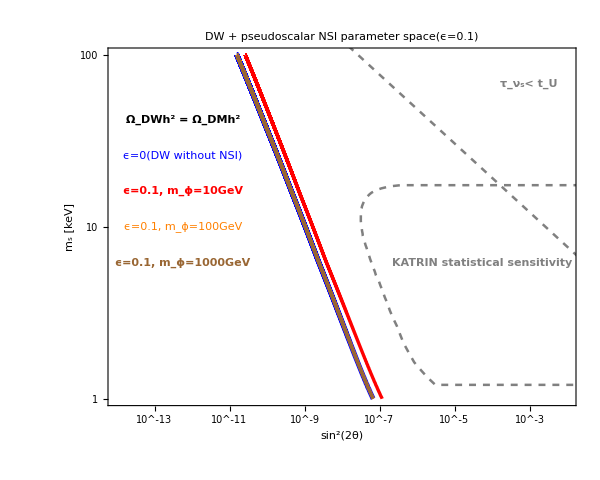

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space(ϵ=0.1)"}],
Prolog->{Blue,Thick,Thickness[0.006],Line[pseudoscalar0],
Red,Thick,Thickness[0.004],Line[pseudoscalar0110],
Orange,Thick,Thickness[0.004],Line[pseudoscalar01100],
Brown,Thick,Thickness[0.004],Line[pseudoscalar011000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0(DW without NSI)"],-0 Degree],Scaled[{0.16,0.7}]],
Orange, Text[Rotate[Style["ϵ=0.1, m_ϕ=100GeV"],-0 Degree],Scaled[{0.16,0.5}]],
Red, Text[Rotate[Style["ϵ=0.1, m_ϕ=10GeV", Bold],-0 Degree],Scaled[{0.16,0.6}]],
Brown, Text[Rotate[Style["ϵ=0.1, m_ϕ=1000GeV", Bold],-0 Degree],Scaled[{0.16,0.4}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Parameter space for ϵ =1 (m_ϕ= 10,100,1000GeV)

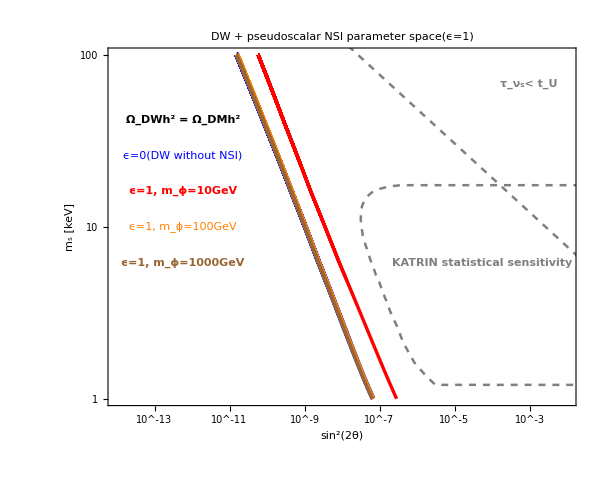

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space(ϵ=1)"}],
Prolog->{Blue,Thick,Thickness[0.006],Line[pseudoscalar0],
Red,Thick,Thickness[0.004],Line[pseudoscalar110],
Orange,Thick,Thickness[0.004],Line[pseudoscalar1100],
Brown,Thick,Thickness[0.004],Line[pseudoscalar11000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0(DW without NSI)"],-0 Degree],Scaled[{0.16,0.7}]],
Orange, Text[Rotate[Style["ϵ=1, m_ϕ=100GeV"],-0 Degree],Scaled[{0.16,0.5}]],
Red, Text[Rotate[Style["ϵ=1, m_ϕ=10GeV", Bold],-0 Degree],Scaled[{0.16,0.6}]],
Brown, Text[Rotate[Style["ϵ=1, m_ϕ=1000GeV", Bold],-0 Degree],Scaled[{0.16,0.4}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Parameter space for ϵ =10 (m_ϕ= 10,100,1000GeV)

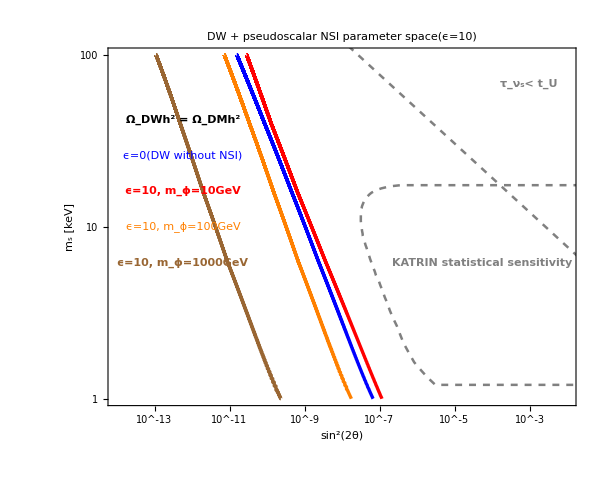

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space(ϵ=10)"}],
Prolog->{Blue,Thick,Thickness[0.004],Line[pseudoscalar0],
Red,Thick,Thickness[0.004],Line[pseudoscalar1010],
Orange,Thick,Thickness[0.004],Line[pseudoscalar10100],
Brown,Thick,Thickness[0.004],Line[pseudoscalar101000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0(DW without NSI)"],-0 Degree],Scaled[{0.16,0.7}]],
Orange, Text[Rotate[Style["ϵ=10, m_ϕ=100GeV"],-0 Degree],Scaled[{0.16,0.5}]],
Red, Text[Rotate[Style["ϵ=10, m_ϕ=10GeV", Bold],-0 Degree],Scaled[{0.16,0.6}]],
Brown, Text[Rotate[Style["ϵ=10, m_ϕ=1000GeV", Bold],-0 Degree],Scaled[{0.16,0.4}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Parameter space for ϵ =100 (m_ϕ= 10,100,1000GeV)

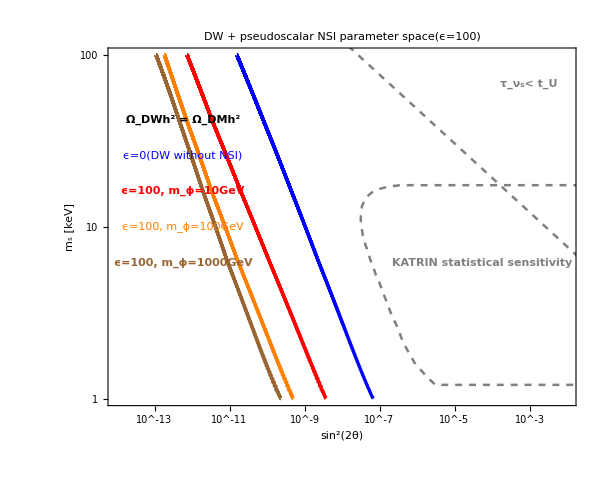

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space(ϵ=100)"}],
Prolog->{Blue,Thick,Thickness[0.004],Line[pseudoscalar0],
Red,Thick,Thickness[0.004],Line[pseudoscalar10010],
Orange,Thick,Thickness[0.004],Line[pseudoscalar100100],
Brown,Thick,Thickness[0.004],Line[pseudoscalar1001000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0(DW without NSI)"],-0 Degree],Scaled[{0.16,0.7}]],
Orange, Text[Rotate[Style["ϵ=100, m_ϕ=100GeV"],-0 Degree],Scaled[{0.16,0.5}]],
Red, Text[Rotate[Style["ϵ=100, m_ϕ=10GeV", Bold],-0 Degree],Scaled[{0.16,0.6}]],
Brown, Text[Rotate[Style["ϵ=100, m_ϕ=1000GeV", Bold],-0 Degree],Scaled[{0.16,0.4}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Parameter space for ϵ =1000 (m_ϕ= 10,100,1000GeV)

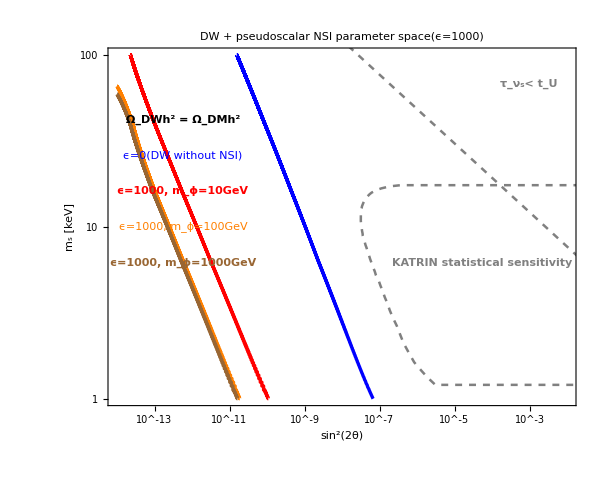

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space(ϵ=1000)"}],
Prolog->{Blue,Thick,Thickness[0.004],Line[pseudoscalar0],
Red,Thick,Thickness[0.004],Line[pseudoscalar100010],
Orange,Thick,Thickness[0.004],Line[pseudoscalar1000100],
Brown,Thick,Thickness[0.004],Line[pseudoscalar10001000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0(DW without NSI)"],-0 Degree],Scaled[{0.16,0.7}]],
Orange, Text[Rotate[Style["ϵ=1000, m_ϕ=100GeV"],-0 Degree],Scaled[{0.16,0.5}]],
Red, Text[Rotate[Style["ϵ=1000, m_ϕ=10GeV", Bold],-0 Degree],Scaled[{0.16,0.6}]],
Brown, Text[Rotate[Style["ϵ=1000, m_ϕ=1000GeV", Bold],-0 Degree],Scaled[{0.16,0.4}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Parameter space for ϵ =- 0.1 (m_ϕ= 10,100,1000GeV)

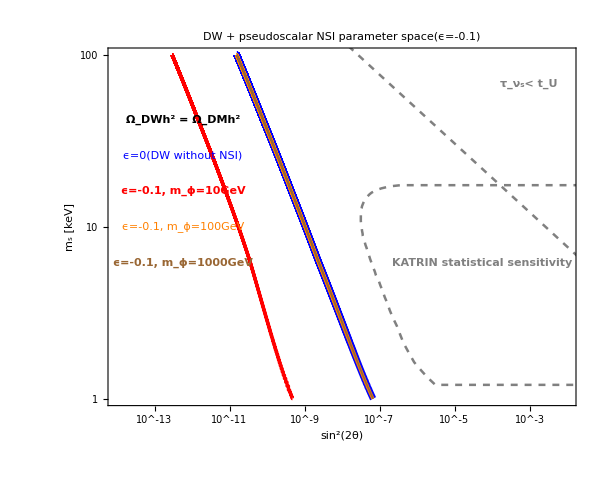

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space(ϵ=-0.1)"}],
Prolog->{Blue,Thick,Thickness[0.008],Line[pseudoscalar0],
Red,Thick,Thickness[0.004],Line[pseudoscalarn0110],
Orange,Thick,Thickness[0.004],Line[pseudoscalarn01100],
Brown,Thick,Thickness[0.002],Line[pseudoscalarn011000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0(DW without NSI)"],-0 Degree],Scaled[{0.16,0.7}]],
Orange, Text[Rotate[Style["ϵ=-0.1, m_ϕ=100GeV"],-0 Degree],Scaled[{0.16,0.5}]],
Red, Text[Rotate[Style["ϵ=-0.1, m_ϕ=10GeV", Bold],-0 Degree],Scaled[{0.16,0.6}]],
Brown, Text[Rotate[Style["ϵ=-0.1, m_ϕ=1000GeV", Bold],-0 Degree],Scaled[{0.16,0.4}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Parameter space for ϵ =- 1 (m_ϕ= 10,100,1000GeV)

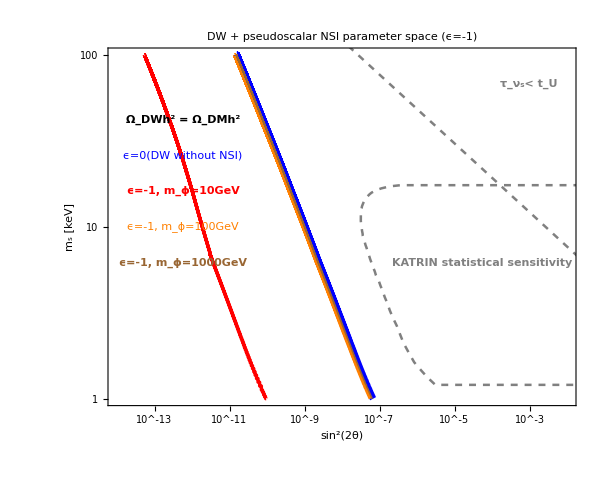

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space (ϵ=-1)"}],
Prolog->{Blue,Thick,Thickness[0.008],Line[pseudoscalar0],
Red,Thick,Thickness[0.004],Line[pseudoscalarn110],
Orange,Thick,Thickness[0.004],Line[pseudoscalarn1100],
Brown,Thick,Thickness[0.002],Line[pseudoscalarn11000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.16,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0(DW without NSI)"],-0 Degree],Scaled[{0.16,0.7}]],
Orange, Text[Rotate[Style["ϵ=-1, m_ϕ=100GeV"],-0 Degree],Scaled[{0.16,0.5}]],
Red, Text[Rotate[Style["ϵ=-1, m_ϕ=10GeV", Bold],-0 Degree],Scaled[{0.16,0.6}]],
Brown, Text[Rotate[Style["ϵ=-1, m_ϕ=1000GeV", Bold],-0 Degree],Scaled[{0.16,0.4}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Plots for m_ϕ=10 GeV

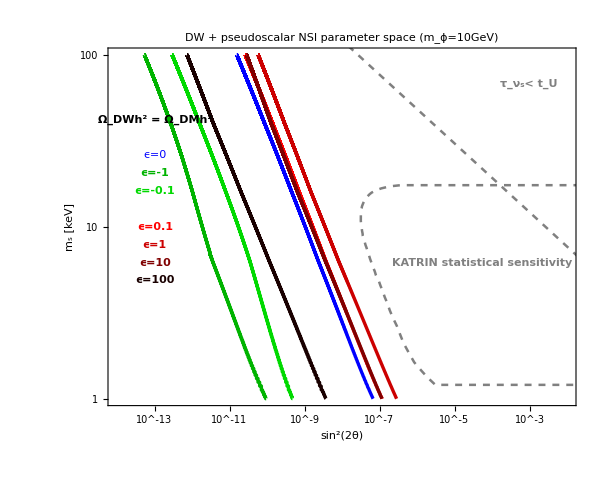

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space (m_ϕ=10GeV)"}],
Prolog->{Blue,Thick,Thickness[0.004],Line[pseudoscalar0],
Darker[Green,0.3],Thick,Thickness[0.004],Line[pseudoscalarn110],
Darker[Green,0.15],Thick,Thickness[0.004],Line[pseudoscalarn0110],
Darker[Red,0],Thick,Thickness[0.004],Line[pseudoscalar0110],
Darker[Red,0.2],Thick,Thickness[0.004],Line[pseudoscalar110],
Darker[Red,0.5],Thick,Thickness[0.004],Line[pseudoscalar1010],
Darker[Red,0.9],Thick,Thickness[0.004],Line[pseudoscalar10010],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.1,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0"],-0 Degree],Scaled[{0.1,0.7}]],
Darker[Green,0.3], Text[Rotate[Style["ϵ=-1", Bold],-0 Degree],Scaled[{0.1,0.65}]],
Darker[Green,0.15], Text[Rotate[Style["ϵ=-0.1", Bold],-0 Degree],Scaled[{0.1,0.6}]],
Darker[Red,0], Text[Rotate[Style["ϵ=0.1", Bold],-0 Degree],Scaled[{0.1,0.5}]],
Darker[Red,0.2], Text[Rotate[Style["ϵ=1", Bold],-0 Degree],Scaled[{0.1,0.45}]],
Darker[Red,0.5], Text[Rotate[Style["ϵ=10", Bold],-0 Degree],Scaled[{0.1,0.4}]],
Darker[Red,0.9], Text[Rotate[Style["ϵ=100", Bold],-0 Degree],Scaled[{0.1,0.35}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Plots for m_ϕ=100 GeV

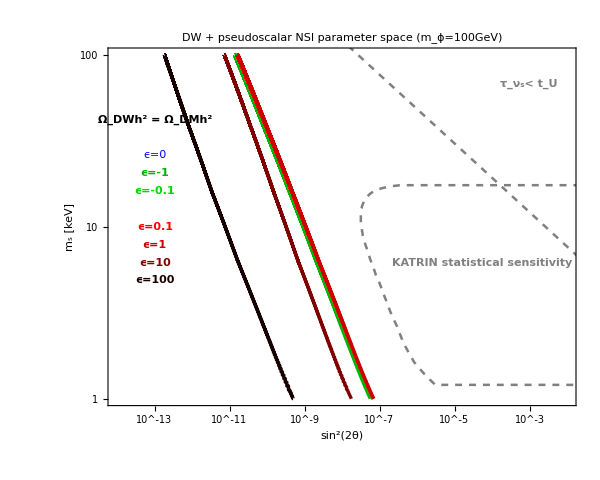

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space (m_ϕ=100GeV)"}],
Prolog->{Blue,Thick,Thickness[0.004],Line[pseudoscalar0],
Darker[Green,0.3],Thick,Thickness[0.004],Line[pseudoscalarn1100],
Darker[Green,0.15],Thick,Thickness[0.004],Line[pseudoscalarn01100],
Darker[Red,0],Thick,Thickness[0.004],Line[pseudoscalar01100],
Darker[Red,0.2],Thick,Thickness[0.004],Line[pseudoscalar1100],
Darker[Red,0.5],Thick,Thickness[0.004],Line[pseudoscalar10100],
Darker[Red,0.9],Thick,Thickness[0.004],Line[pseudoscalar100100],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.1,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0"],-0 Degree],Scaled[{0.1,0.7}]],
Darker[Green,0.3], Text[Rotate[Style["ϵ=-1", Bold],-0 Degree],Scaled[{0.1,0.65}]],
Darker[Green,0.15], Text[Rotate[Style["ϵ=-0.1", Bold],-0 Degree],Scaled[{0.1,0.6}]],
Darker[Red,0], Text[Rotate[Style["ϵ=0.1", Bold],-0 Degree],Scaled[{0.1,0.5}]],
Darker[Red,0.2], Text[Rotate[Style["ϵ=1", Bold],-0 Degree],Scaled[{0.1,0.45}]],
Darker[Red,0.5], Text[Rotate[Style["ϵ=10", Bold],-0 Degree],Scaled[{0.1,0.4}]],
Darker[Red,0.9], Text[Rotate[Style["ϵ=100", Bold],-0 Degree],Scaled[{0.1,0.35}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Plots for m_ϕ=1000 GeV

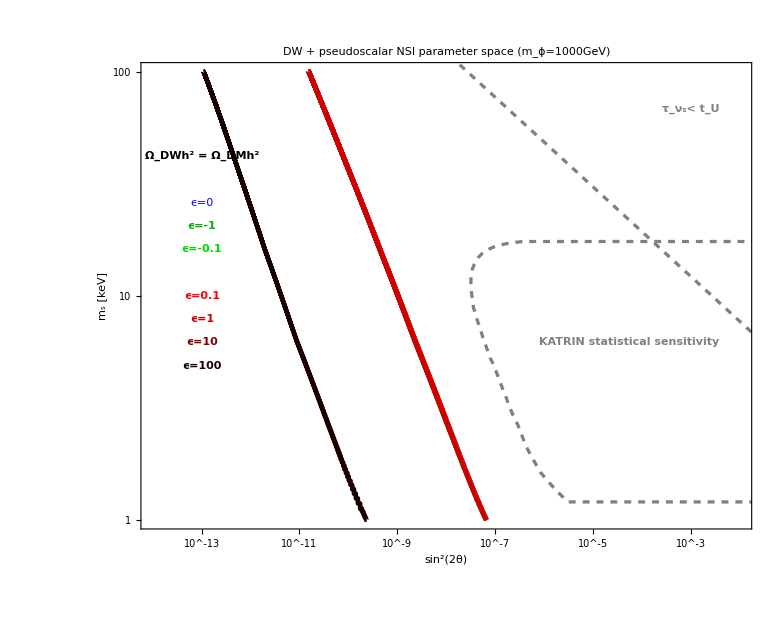

```mathematica
parameterspace=Plot[{},{x,-16,-3},PlotRange->{{-14, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],20,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],20,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, PlotLabel->Row[{
"DW + pseudoscalar NSI parameter space (m_ϕ=1000GeV)"}],
Prolog->{Blue,Thick,Thickness[0.004],Line[pseudoscalar0],
Darker[Green,0.3],Thick,Thickness[0.004],Line[pseudoscalarn11000],
Darker[Green,0.15],Thick,Thickness[0.004],Line[pseudoscalarn011000],
Darker[Red,0],Thick,Thickness[0.004],Line[pseudoscalar011000],
Darker[Red,0.2],Thick,Thickness[0.004],Line[pseudoscalar11000],
Darker[Red,0.5],Thick,Thickness[0.004],Line[pseudoscalar101000],
Darker[Red,0.9],Thick,Thickness[0.004],Line[pseudoscalar1001000],
Gray,Dashed,Thickness[0.003],Line[KATstatIlog],
Gray,Dashed,Thickness[0.003],Line[mainchannelboundlog]
 },

Epilog->{FontSize->16,
Black, Text[Rotate[Style["Ω_DWh^2 = Ω_DMh^2",Bold],-0 Degree,Bold],Scaled[{0.1,0.8}]],
FontSize->12,
Blue, Text[Rotate[Style["ϵ=0"],-0 Degree],Scaled[{0.1,0.7}]],
Darker[Green,0.3], Text[Rotate[Style["ϵ=-1", Bold],-0 Degree],Scaled[{0.1,0.65}]],
Darker[Green,0.15], Text[Rotate[Style["ϵ=-0.1", Bold],-0 Degree],Scaled[{0.1,0.6}]],
Darker[Red,0], Text[Rotate[Style["ϵ=0.1", Bold],-0 Degree],Scaled[{0.1,0.5}]],
Darker[Red,0.2], Text[Rotate[Style["ϵ=1", Bold],-0 Degree],Scaled[{0.1,0.45}]],
Darker[Red,0.5], Text[Rotate[Style["ϵ=10", Bold],-0 Degree],Scaled[{0.1,0.4}]],
Darker[Red,0.9], Text[Rotate[Style["ϵ=100", Bold],-0 Degree],Scaled[{0.1,0.35}]],
FontSize->12,
Gray, Text[Rotate[Style["KATRIN statistical sensitivity", Bold],-0 Degree],Scaled[{0.8,0.4}]],
FontSize->20,
Gray, Text[Rotate[Style["τ_ν_s< t_U", Bold],-0 Degree],Scaled[{0.9,0.9}]]},

FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```